10201

5.92875×10^6

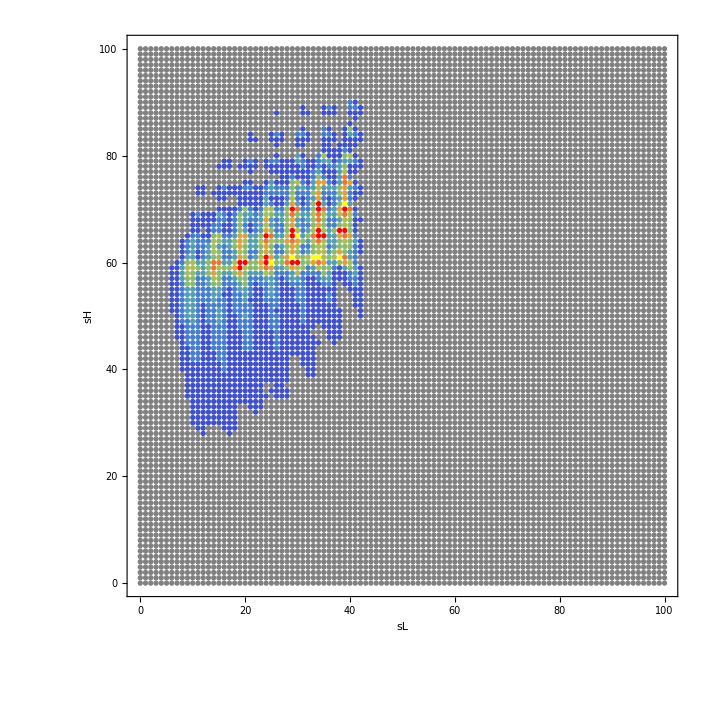

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[tickFunction,tickFunctionNoLabel,gridFunction,divisionFunction]
nx=100;ny=100;graf={};
diskord=Import["dedf3/HistPlot-s-2.dat","Table"];discord=Flatten[diskord];
Print[Length[discord]];
kount = 0;
xmd=Max[discord];
Print[Max[discord]];
For[i=0,i≤nx,i++,
{
For[j=0,j≤ny,j++,
{
kount+=1;k1 = i;k2=j;k3=kount;
discord[[k3]]=IntegerPart[10*discord[[k3]]/xmd]+1;
If[discord[[k3]]==1 ,coll=LightGray];
If[discord[[k3]]==2 ,coll=Purple];
If[discord[[k3]]==3 ,coll=Brown];
If[discord[[k3]]==4 ,coll=Red];
If[discord[[k3]]==5 ,coll=Magenta];
If[discord[[k3]]==6 ,coll=Gray];
If[discord[[k3]]==7 ,coll=Blue];
If[discord[[k3]]==8 ,coll=LightBlue];
If[discord[[k3]]==9 ,coll=Green];
If[discord[[k3]]==10,coll=Yellow];

If[discord[[k3]]==1 ,coll=Gray];
If[discord[[k3]]==2 ,coll=RGBColor[63/255,80/255,204/255]];
If[discord[[k3]]==3 ,coll=RGBColor[68/255,126/255,204/255]];
If[discord[[k3]]==4 ,coll=RGBColor[84/255,158/255,178/255]];
If[discord[[k3]]==5 ,coll=RGBColor[138/255,187/255,107/255]];
If[discord[[k3]]==6 ,coll=RGBColor[172/255,190/255,81/255]];
If[discord[[k3]]==7 ,coll=RGBColor[225/255,160/255,58/255]];
If[discord[[k3]]==8 ,coll=RGBColor[231/255,119/255,49/255]];
If[discord[[k3]]==9 ,coll=Red];
If[discord[[k3]]==10,coll=Yellow];
graf=Append[graf,{coll,Disk[{k1,k2},{.5,.5}]}];
}
];
}
];

divisionFunction[xMin_,xMax_]:=FindDivisions[{xMin,xMax},{8,5}];

gridFunction[xMin_,xMax_]:=First[divisionFunction[xMin,xMax]]

Options[tickFunction]={"MinorLength"->0.005,"MajorLength"->.01,"InsideOutside"->{1,0}};

tickFunction[xMin_,xMax_,OptionsPattern[]]:=Module[{major,minor},{major,minor}=divisionFunction[xMin,xMax];
Join[Map[{#,#,OptionValue["InsideOutside"] OptionValue["MajorLength"]}&,major],Map[{#,"",OptionValue["InsideOutside"] OptionValue["MinorLength"]}&,Flatten[minor[[All,2;;-2]]]]]]

tickFunctionNoLabel[xMin_,xMax_]:=Map[{#[[1]],"",#[[-1]]}&,tickFunction[xMin,xMax]]

SetOptions[Plot,FrameTicks->{{tickFunction,tickFunctionNoLabel},{tickFunctionNoLabel,tickFunction}}];
GR1=Show[
Graphics[graf],
(*
Graphics[statgraf],
*)
Frame->True,
PlotRange->{{-.5,nx+.5},{-.5,ny+.5}},
FrameLabel->{{"sH",},{"sL",}} ,
FrameTicks->{{tickFunction,tickFunction},{tickFunction,tickFunction}},
LabelStyle->Directive["Helvetica",Bold,14],
ImageSize->10 {nx/1.5+4,nx/1.5+4}
];
GR1
```